# Метод на допирателните (Нютон) за 67ми номер

## Дадено е уравнението: (x^2 - x + a)/(x^3 - 7) + 5/(a +b + 1) = 0

```mathematica
f[x_] := (x^2 - x + 6)/(x^3 - 7) + 5/14
```

```mathematica
f[x]
```

5/14+(6-x+x^2)/(-7+x^3)

### 1. Да се намери броят на корените на уравнението и да се локализира най-малкият от тях (в случай на повече от един)

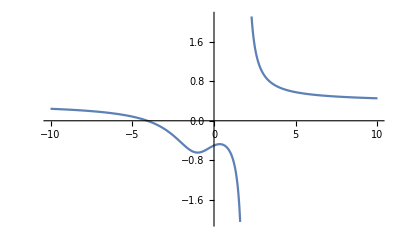

```mathematica
Plot[f[x], {x, -10, 10}]
```

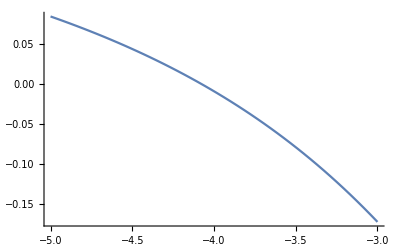

```mathematica
Plot[f[x], {x, -5, -3}]
```

Брой корени: 1

Локализация на най-малкия корен

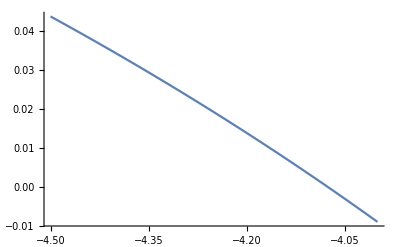

```mathematica
Plot[f[x], {x, -4.5, -4}]
```

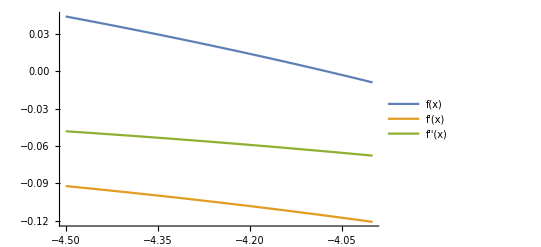

```mathematica
Plot[{f[x], f'[x], f''[x]}, {x, -4.5, -4}, PlotLegends->"Expressions"]
```

```mathematica
f[-4.5]
```

0.0437671

```mathematica
f[-4.]
```

-0.00905433

Извод:
1. f(-4.5) = 0.0437... > 0
2. f(-5.5) = -0.0090... < 0
Следователно в двата края на функцията има различни знаци и функцията е непрекъсната в избрания интервал [-4.5;-4].
Следва, че функцията има поне един корен в дадения интервал.

### 2. Да се проверят условията на метода на Нютон

#### Проверка на първата производна

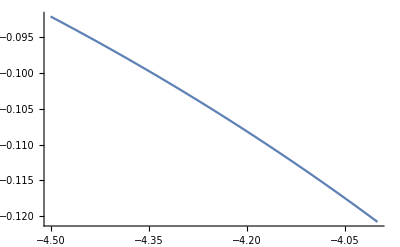

```mathematica
Plot[f'[x], {x, -4.5, -4}]
```

Извод: (1) Стойностите на първата производна в разглеждания интервал [-4.5;-4] са между -0.122 и -0.093. Следователно първата f'(x) < 0 в целия разглеждан интервал [-4.5;-4].

#### Проверка на втората производна

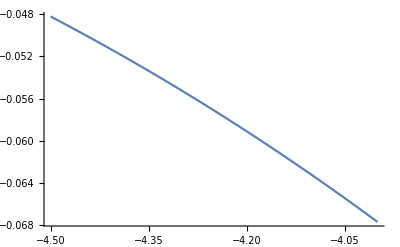

```mathematica
Plot[f''[x], {x, -4.5, -4}]
```

Извод: (2) Стойностите на първата производна в разглеждания интервал [-4.5;-4] са между -0.068 и -0.048. Следователно втората f''(x) < 0 в целия разглеждан интервал [-4.5;-4].

Извод: от (1) и (2) следва, че f'(x) и f''(x) са с постоянни знаци в разглеждания интервал [-4.5;-4] => Методът на допирателните е сходящ.

### 3. Да се направят 3 итерации по метода на Нютон

???

### 4. Каква е грешката на полученото решение?

???

### 5. Колко итерации са необходими за достигане на точност 10^-5?

```mathematica
f[x_] := (x^2 - x + 6)/(x^3 - 7) + 5/14
x0 = -4;
М2 = Abs[f''[-4]];
m1 = Abs[f'[4.5]];
p = М2/(2m1);
epszad = 0.00001;
eps = 1;
Print["n = ",0,  " x_n = ", N[x0], " f(x) = ", N[f[x0]], " f'(x) = ", N[f'[x0]]];
For[n = 1, eps > epszad, n++,
x1 = x0 - f[x0]/f'[x0];
Print["n = ",n,  " x_n = ", N[x1], " f(x_n) = ", N[f[x1]] " f'(x_n) = ", N[f'[x1]], " ε_n = ", N[eps = p* (x1 - x0)^2]];
x0 = x1
]
```

n = 0 x_n = -4. f(x) = -0.00905433 f'(x) = -0.120809

n = 1 x_n = -4.07495 f(x_n) = -0.00018705  f'(x_n) = -0.11586 ε_n = 0.00207654

n = 2 x_n = -4.07656 f(x_n) = -8.38657×10^-8  f'(x_n) = -0.115756 ε_n = 9.63561×10^-7

### 6. Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [p, q] за същата точност

```mathematica
Log2[(-4+ 4.5)/0.00001] - 1
```

14.6096

### 7. Да се направи сравнение кой метод е по-ефективен за избрания интервал

Извод: По метода на допирателните (Нютон) биха били необходими 2 итерации за достигане на исканата точност. А по метода на разполовяването са необходими 15 итерации. Следователно методът на допирателните е по-ефективен за избрания интервал [-4.5, -4].